# Means

Plotting mean distribution and velocity values as a function of printing parameters and matching experimental processing-structure correlations to theoretical correlations.
Used for “Changes in filament microstructures during direct ink writing with yield stress fluid support”
Last updated November 2019 by Leanne Friedrich

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
bigtable2 = Import["Tables\\bigtable2_middleedge.csv"];
changetable = Import["Tables\\changetable_middleedge.csv"];
<<"Mathematica\\means.wl"
```

## transitions

This figure shows transitions in the particle distribution width and position between passes around the polygon

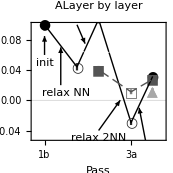
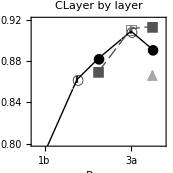
-Graphics--Graphics--Graphics--Graphics--Graphics-
●○ | Line 1
■□ | Line 2
▲ | Line 3

```mathematica
elpset = elpsettings;
elpset["pmode"] = 2;
lp = 38; (*left padding*)
rp = 1; (*right padding*)
is = (6.5*72 - 45 - 2*lp-2*rp)/4; (*image size*)
transitionsfigure = Row[Append[
Flatten[
Table[Table[
elpset["title"] =(
Row[{
Pane[s12[#[[1]]], ImageSize->14*PS, Alignment->Left]
, Pane[s8[#[[2]]], ImageSize->(is-2*14)*PS, Alignment->Center]
, Pane["", ImageSize->14*PS, Alignment->Left]}]
&/@{ {"A", "Layer by layer"}, {"B","Bath"}, {"C","Layer by layer"}, {"D","Bath"}}
)[[i+2*(j-1)]];
elpset["left"] = i==1;
elpset["pr"] = {{0.8, 3.2},{{-0.05, 0.1}, {0.80, 0.92}}[[j]]};
plot = Show[plotallpositions[Select[bigtable2, #[[3]]==({2,3}[[i]])&], {1,3}[[j]], {1,2,3}, 4, elpset]
, PlotRangePadding->{{0,0}, {Scaled[0.2], Scaled[0.1]}}];
If[i==1&&j==1
, plot = Show[plot
		, Graphics[{Text[s8["init"], {1, 0.05}], Arrow[{{1, 0.06},{1,0.085}}]
				, Text[s8["relax NN"], {1.4, 0.01}], Arrow[{{1.3, 0.02},{1.3,0.07}}]
				, Text[s8["shear"], {1.6, 0.11}], Arrow[{{1.6, 0.1},{1.75,0.075}}]
				, Text[s8["relax 2NN"], {2, -0.05}], Arrow[{{2, -0.04},{2.4, 0}}]
				, Text[s8["shear"], {2.88, -0.08}], Arrow[{{2.9,-0.065},{2.75,-0.01}}]
		}]
		]
];
If[i==2&&j==1
, plot = Show[plot
		,Graphics[{ Text[s8@"↓outer", {0.9, -0.07}, Left]
				,Text[s8@"↑inner", {0.9, 0.1}, Left]
				, Text[s8@"ideal", {1,-0.02}, Left]
				, Arrow[{{0.95, -0.02}, {0.87, 0}}]
		}]
		]
];
If[i==2&&j==2
, plot = Show[plot
		,Graphics[{ Text[s8@"↓narrow, ideal", {0.9, 0.78}, Left]
				,Text[s8@"↑wide", {0.9,0.92}, Left]}]
		]
];
plot
,{i,2}], {j, 2}]
]
,(*legend*) 
Column[{
Graphics[{FaceForm[None]
		,EdgeForm[{Thick,GrayLevel[0.66]}], Polygon[CirclePoints[5]*1]
		,EdgeForm[{Thick,GrayLevel[0.33]}], Polygon[CirclePoints[5]*0.75]
		,EdgeForm[{Thick,GrayLevel[0]}], Polygon[CirclePoints[5]*0.5]
}, ImageSize->45]
, Grid[{
{Style["●○", GrayLevel[0]],  s8c["Line 1", GrayLevel[0]]}
, {Style["■□", GrayLevel[0.33]],s8c["Line 2", GrayLevel[0.33]]}
,{Style["▲", GrayLevel[0.66]], s8c["Line 3", GrayLevel[0.66]]}
}, Alignment->Left]
}]
]]
```

```mathematica
Export["Figures\\transitionsm.pdf", transitionsfigure];
```

## Kendall tests: dependent variables vs. independent variables

#### Velocities

```mathematica
ktable = ConstantArray["", {10*4*2+1, 8}];
kindex = 1;
ktable[[kindex]] = {"region", "region num", "x var", "sup", "tau", "p", "sign+", "sign", "significant"};
kindex = kindex+1;
Do[
Do[
Do[
kendall = If[xvar==0,tpkmean[m, bigtable2, yvar, 2], tpkvar[m, bigtable2, xvar, yvar,2]];
ktable[[kindex]] = Join[{REGIONLIST[[(yvar-9)/2]], yvar, xvar, Switch[m, 2, "LBL", 3, "Bath"]}, kendall];
kindex = kindex+1;
,{m, {3,2}}];
, {yvar, 11, 29, 2}];
,{xvar, {0, 9, 1, 2}}];
Export["Tables\\kvectable.csv",ktable];
```

#### Distributions

```mathematica
ktable = ConstantArray["", {8*4*2+1, 8}];
kindex = 1;
ktable[[kindex]] = {"dist", "dist mode", "x var", "sup", "tau", "p", "sign+", "sign", "significant"};
kindex = kindex+1;
Do[
Do[
Do[
tpk = tpkdist[bigtable2, changetable, mmode, xvar, m, 2];
If[Length[tpk]>0,
ktable[[kindex]] = Join[{label[mmode], mmode, xvar, Switch[m, 2, "LBL", 3, "Bath"]}, tpk];
kindex = kindex+1;
,
ktable[[kindex]] = Join[{label[mmode], mmode, xvar, Switch[m, 2, "LBL", 3, "Bath"]}, ConstantArray["", 5]];
kindex = kindex+1;
];
,{m, {3,2}}];
, {mmode, 1, 8}];
,{xvar, {0, 9, 1, 2}}];
Export["Tables\\kdisttable.csv",ktable];
```

#### Final distributions

```mathematica
ktable = ConstantArray["", {10*4*2+1, 8}];
kindex = 1;
ktable[[kindex]] = {"dist", "dist mode", "x var", "sup", "tau", "p", "sign+", "sign", "significant"};
kindex = kindex+1;
Do[
Do[
Do[
tpk =Switch[xvar,0,finalposave[bigtable2, m,pos, 2],9,finalpospass[bigtable2, m,pos, 2],_, finalpossplit[bigtable2, m, pos, xvar, 2]];
ktable[[kindex]] = Join[{"final "<>If[pos, "pos", "w"], 31+If[pos,0,1], xvar, Switch[m, 2, "LBL", 3, "Bath"]}, tpk];
kindex = kindex+1;
,{m, {3, 2}}];
, {xvar, {0,9, 1, 2}}]
, {pos, {True , False}}];
Export["Tables\\kfinaltable.csv",ktable];
```

## Transverse flow plots

```mathematica
kvecs = Import["Tables\\kvectable.csv"];
```

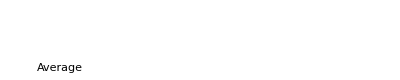
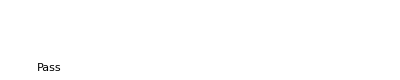
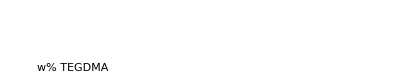
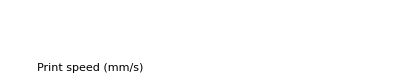
○ Layer-by-layer  ● Bath
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-

```mathematica
vtplots = vplotcol[{0,9,1,2}, kvecs, bigtable2]
Export["Figures\\vtplot.pdf", vtplots];
```

```mathematica
vtplotline = vplotcol[{9}, kvecs, bigtable2]
Export["Figures\\vpass.pdf", vtplotline];
```

○ Layer-by-layer  ● Bath
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-

## dist results lists

```mathematica
kdist = Import["Tables\\kdisttable.csv"];
```

```mathematica
tlist2 = {"Position (mm)", "Width (normalized)"};
headerlist = Row[Table[Graphics[Style[Text[tlist2[[i]]], 8*PS, FontFamily->"Arial"], ImageSize->{Round[(3.25*72)*PS],10}], {i,2}]];
distplots = 
Column[
{plegend[Row]
,
headerlist
,
Row[Table[
Column[Table[
Row[Table[
tp = Table[tpkdist[bigtable2, changetable, mmode, xvar, m, 1],{m, {3,2}}];
kendall = SortBy[Select[kdist, #[[2]]==mmode && #[[3]]==xvar&], #[[4]]&][[;;, 5;;]];
distplot[xvar,mmode, kendall, tp]
,{xvar, {0, 9, 1, 2}}]]
, {mmode,1+d,4+d}]]
,{d, {0,4}}]]
}, Alignment->Right]
```

○ Layer-by-layer  ● Bath
-Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Export["Figures\\distplots2.pdf",distplots];
```

## final

```mathematica
kfinal = Import["Tables\\kfinaltable.csv"];
```

```mathematica
finalplots = 
Column[{plegend[Row],
Row[
Table[Row[Table[
tp =Table[
Switch[xvar,0,finalposave[bigtable2, m,pos, 1],9,finalpospass[bigtable2, m,pos, 1],_, finalpossplit[bigtable2, m, pos, xvar, 1]]
,{m, {3,2}}];
kendall = SortBy[Select[kfinal, #[[2]]==If[pos, 31, 32] && #[[3]]==xvar&], #[[4]]&][[;;, 5;;]];
finalplot[xvar,kendall, tp, pos]
, {xvar, {0,9, 1, 2}}]], {pos, {True , False}}]
]}, Alignment->Right]
```

○ Layer-by-layer  ● Bath
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Export["Figures\\finalplots.pdf", finalplots];
```

## comparing theory to experiments

```mathematica
theotable = Import["Tables\\theorymasterstraights.xlsx"][[1]];
rr = importrr["Tables\\replacementrules.xlsx"];
```

### theory latex tables

```mathematica
theory2latex[theotable, 1, True, rr]
```

Figures\vtheory_Plastic_zone_flow.txt

Figures\dtheory_Plastic_zone_flow.txt

Figures\listtheory_Plastic_zone_flow.txt

Figures\vtheory_Disturbed_zone.txt

Figures\dtheory_Disturbed_zone.txt

Figures\listtheory_Disturbed_zone.txt

Figures\vtheory_Capillary_spreading.txt

Figures\dtheory_Capillary_spreading.txt

Figures\listtheory_Capillary_spreading.txt

Figures\vtheory_Gravity_spreading.txt

Figures\dtheory_Gravity_spreading.txt

Figures\listtheory_Gravity_spreading.txt

Figures\vtheory_Particle_settling.txt

Figures\dtheory_Particle_settling.txt

Figures\listtheory_Particle_settling.txt

```mathematica
theory2latex[theotable, 2, True, rr]
```

figures\boththeory_Plastic_zone_flow.txt

figures\boththeory_Disturbed_zone.txt

figures\boththeory_Capillary_spreading.txt

figures\boththeory_Gravity_spreading.txt

figures\boththeory_Particle_settling.txt

### experiment latex tables

```mathematica
kdist =Import["Tables\\kdisttable.csv"];
kvecs = Import["Tables\\kvectable.csv"];
```

```mathematica
Export["Figures\\bothresults.txt", exp2latex[kvecs, kdist]]
```

Figures\bothresults.txt

### matches between theory and experiment

```mathematica
Export["Figures\\matchesv.txt", matches[kvecs, kdist, 1]]
Export["Figures\\matchesd.txt", matches[kvecs, kdist,2]]
```

Figures\matchesv.txt

Figures\matchesd.txt

### numerical matches

```mathematica
vindices = {{1},{2},{3},{4},{5},{6,7},{8},{9,10}};
vheader =  { "ahead", "nozzle", "just behind", "behind outer", "far behind", "behind right", "outer", "right"};
dindices = {{11,15},{12,16},{13,17},{14,18}};
dheader = { "Initial", "$\\Delta$relax NN","$\\Delta$relax 2NN","$\\Delta$shear"};
t3 = matchesnumadd[theotable, kvecs, kdist, vindices,dindices,vheader,dheader];
Export["figures\\matchessimplenumlong.txt", t3]
```

figures\matchessimplenumlong.txt

```mathematica
vindices = {{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}};
vheader =  { "ahead", "nozzle", "just behind", "behind outer", "far behind", "behind NN","behind 2NN", "outer", "NN","2NN"};
dindices = {{11},{15},{12},{13},{16},{17},{14},{18}};
dheader = { "Initial pos","Initial width", "$\\Delta$ pos relax NN","$\\Delta$ pos relax 2NN", "$\\Delta$ width relax NN", "$\\Delta$ width relax 2NN", "$\\Delta$pos shear", "$\\Delta$width shear"};
t3 = matchesnumadd[theotable, kvecs, kdist, vindices,dindices,vheader,dheader];
Export["figures\\matchessimplenumlong2.txt", t3]
```

figures\matchessimplenumlong2.txt